```mathematica
RandomWeightedGraphTriangleInequality[vertices_,threshhold_]:=Module[{randomGraph},randomGraph=RandomGraph[SpatialGraphDistribution[vertices,threshhold]];Graph[randomGraph,EdgeWeight->Thread[EdgeList[randomGraph]->(EuclideanDistance[AnnotationValue[{randomGraph,First[#]},VertexCoordinates],AnnotationValue[{randomGraph,Last[#]},VertexCoordinates]]&/@EdgeList[randomGraph])],EdgeLabels->"EdgeWeight",ImageSize->Full]]
```

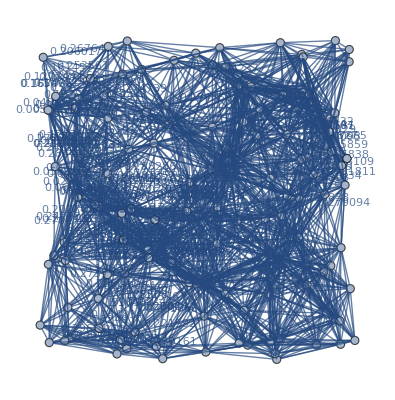

```mathematica
RandomWeightedGraphTriangleInequality[148,.3]
```

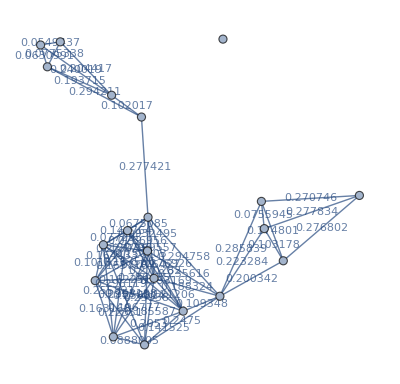

```mathematica
RandomWeightedGraphTriangleInequality[20,.3]
```